# Lotka Volterra Gillespie

### Params

```mathematica
k1=0.01;
k2=0.02;
k3=0.00001;
initA=1000;
initB=1000;
```

```mathematica
<<Gillespie`
```

makeReaction::shdw: Symbol makeReaction appears in multiple contexts {Gillespie`,Global`}; definitions in context Gillespie` may shadow or be shadowed by other definitions.

runGillespie::shdw: Symbol runGillespie appears in multiple contexts {Gillespie`,Global`}; definitions in context Gillespie` may shadow or be shadowed by other definitions.

```mathematica
k1=0.1;
k2=0.18;
k3=0.001;
initA=100;
initB=100;
rxns={makeReaction["r1",k1,{},{"X"}],makeReaction["r2",k2,{"Y"},{}],makeReaction["r3",k3,{"X","Y"},{"Y","Y"}]};
```

```mathematica
countsInit=Association[];
countsInit["X"]=initA;
countsInit["Y"]=initB;
{counts,rxnCounts}=runGillespie[500,countsInit,rxns,{},1.0];
```

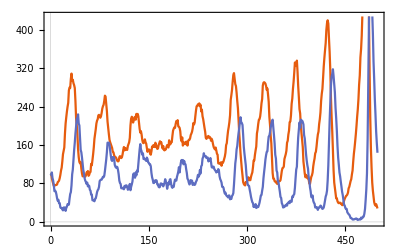

```mathematica
ListLinePlot[{counts["X"],counts["Y"]}]
```

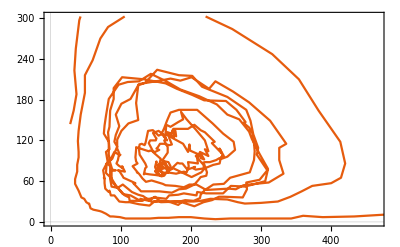

```mathematica
ListLinePlot[Transpose[{counts["X"][[;;,2]],counts["Y"][[;;,2]]}]]
```